```mathematica
(*
Namen je predstavitev tonov, intervalov ter akordov v podmnožici realnega evklidskega prostora R^n, kjer je n število sočasno zvenečih tonov v akordu. Ker sočasno lahko zveni neskončno različnih tonov (v resnici ima vsak zven glasu/inštrumenta neskončno alikvotov, ki so bolj ali manj poudarjeni) bo naš geometrijski prostor neskočno dimnezionalen.
Vseeno si bomo ogledali zgolj objekte v n-dimenzionalnem prostoru.
*)
```

```mathematica
(*
TON lahko predstavimo v prostoru R+ s frekvenco, ki ta ton določa. Za poenostavitev privzamemo, da ton 440Hz določa a.
*)
```

```mathematica
ton = 660 (* v enoti Hz*);
Show[Graphics3D[Point[{440,0,0}],{Boxed->False,Axes->True}],ImageSize->Medium]
Play[Sin[ton 2 Pi t],{t,0,10}]
```

-Graphics3D-

-Graphics-

```mathematica
(*
INTERVAL(ton1,ton2) dveh specifičnih tonov lahko predstavimo kot točko v prostoru (R+)^2, ki predstavlja kartezični frekvenc produkt dveh tonov. Množica vseh dvojic tonov, med katerima je določen določen interval, ponazorimo s premico v tem prostoru.
*)
ton1 = 440;
ton2 = 800;
Show[Graphics3D[Point[{ton1,ton2,0}]],Axes->True]
Play[{Sin[ton2 Pi t],Sin[ton1 Pi t] } ,{t,0,10}]
```

-Graphics3D-

-Graphics-

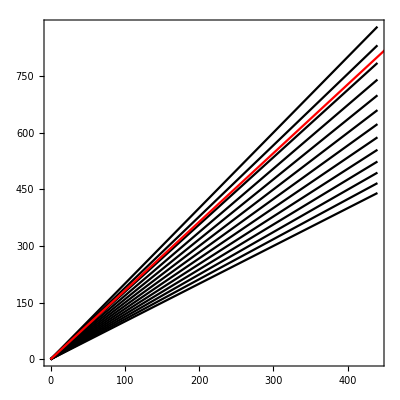

-Graphics3D-

```mathematica
(*CELINTERVAL = INTERVAL(ton1,ton2), ton1, ton2 b R.
Sestavimo množico vseh možnih pozicij intervala za ton1 in ton2, ki sta pozitivni realni števili in prikazujeta frekvenco tonov. To množico predstavimo s premico v (R+)^2
Za intervale predpostavimo temperirano uglasitev *)
CELINTERVAL = ContourPlot[{ton1 y - ton2 x == 0},{x,0,ton1*2},{y,0,ton2 * 2},ContourStyle-> Red ];

tonika= ContourPlot[{y -x == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
malasekunda= ContourPlot[{y -x *2^(1/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
velikasekunda= ContourPlot[{y -x *2^(2/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
malaterca= ContourPlot[{y -x *2^(3/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
velikaterca= ContourPlot[{y -x *2^(4/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
kvarta= ContourPlot[{y -x *2^(5/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
zvkvarta = ContourPlot[{y -x *2^(6/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
kvinta= ContourPlot[{y -x *2^(7/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
malaseksta= ContourPlot[{y -x *2^(8/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
velikaseksta= ContourPlot[{y -x *2^(9/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
malaseptima= ContourPlot[{y -x *2^(10/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
velikaseptima= ContourPlot[{y -x *2^(11/12) == 0},{x,0,ton1},{y,0,880},ContourStyle-> Black ];
oktava= ContourPlot[{y == 2x},{x,0,880},{y,0,880},ContourStyle-> Black ];

CELINTERVAL2 = Graphics3D[Line[{{0,0,0},{ton1,ton2,0}}]];
tonika2 = Graphics3D[Line[{{0,0,0},{1,1,0}}]];
malasekunda2 = Graphics3D[Line[{{0,0,0},{1,2^(1/12),0}}]];
velikasekunda2 = Graphics3D[Line[{{0,0,0},{1,2^(2/12),0}}]];
malaterca2 = Graphics3D[Line[{{0,0,0},{1,2^(3/12),0}}]];
velikaterca2 = Graphics3D[Line[{{0,0,0},{1,2^(4/12),0}}]];
kvarta2 = Graphics3D[Line[{{0,0,0},{1,2^(5/12),0}}]];
zvkvarta2 = Graphics3D[Line[{{0,0,0},{1,2^(6/12),0}}]];
kvinta2 = Graphics3D[Line[{{0,0,0},{1,2^(7/12),0}}]];
malaseksta2 = Graphics3D[Line[{{0,0,0},{1,2^(8/12),0}}]];
velikaseksta2 = Graphics3D[Line[{{0,0,0},{1,2^(9/12),0}}]];
malaseptima2 = Graphics3D[Line[{{0,0,0},{1,2^(10/12),0}}]];
velikaseptima2= Graphics3D[Line[{{0,0,0},{1,2^(11/12),0}}]];
oktava2 = Graphics3D[Line[{{0,0,0},{1,2^(12/12),0}}]];



Show[tonika,malasekunda,velikasekunda,malaterca,velikaterca,kvarta,zvkvarta,kvinta,malaseksta,velikaseksta,malaseptima,velikaseptima,oktava,CELINTERVAL]

Show[tonika2,malasekunda2,velikasekunda2,malaterca2,velikaterca2,kvarta2,zvkvarta2,kvinta2,malaseksta2,velikaseksta2,malaseptima2,velikaseptima2,oktava2,CELINTERVAL2]
```

```mathematica
Show[%495,Axes->True]
```

-Graphics3D-

```mathematica
(*AKORD*)
```

```mathematica
ton1 = 440;
ton2 = 660;
ton3 = 345;
ton4 = 700;
```

```mathematica
Play[{Sin[ton2 Pi t],Sin[ton3 Pi t] ,Sin[ton4 Pi t]} ,{t,0,10}]
```

-Graphics-

```mathematica
Graphics3D[Line[{{0,0,0},{ton1,ton2,ton3}}]]
```

-Graphics3D-

```mathematica
Show[Graphics3D[Line[{{0,0,0},{440,660,345}}]],Axes->True]
```

-Graphics3D-

```mathematica
(*AKORD, več kot 4 toni*)
```

```mathematica
(*ta akord nam predstavlja vektor (ton1,ton2,ton3,ton4) v 4-dimenzionalnem prostoru*)
Play[{Sin[ton2 Pi t],Sin[ton3 Pi t] ,Sin[ton4 Pi t],Sin[ton1 Pi t]} ,{t,0,10}]
```

-Graphics-